### Edit Distance

```mathematica
ClearAll["Global`*"];
(* initialization *)
ED[i_,0]:=i;
ED[0,j_]:=j;
x="polynomial";
y="exponential";
ED[i_,j_]:=ED[i,j]=Module[{c1,c2,c3,best,pos},
c1=If [Characters[x][[i]]==Characters[y][[j]],0,1]+ED[i-1,j-1];
c2=1+ED[i,j-1];
c3=1+ED[i-1,j];
best=Min[c1,c2,c3];
best
];
```

#### Edit distance by dynamic programming

```mathematica
TableForm[Table[ED[i,j],{i,0,10},{j,0,11}],TableHeadings->({""}~Join~#&/@{Characters[x],Characters[y]})]
```

|  | e | x | p | o | n | e | n | t | i | a | l
 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
p | 1 | 1 | 2 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
o | 2 | 2 | 2 | 3 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
l | 3 | 3 | 3 | 3 | 3 | 3 | 4 | 5 | 6 | 7 | 8 | 8
y | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 6 | 7 | 8 | 9
n | 5 | 5 | 5 | 5 | 5 | 4 | 5 | 4 | 5 | 6 | 7 | 8
o | 6 | 6 | 6 | 6 | 5 | 5 | 5 | 5 | 5 | 6 | 7 | 8
m | 7 | 7 | 7 | 7 | 6 | 6 | 6 | 6 | 6 | 6 | 7 | 8
i | 8 | 8 | 8 | 8 | 7 | 7 | 7 | 7 | 7 | 6 | 7 | 8
a | 9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 7 | 6 | 7
l | 10 | 10 | 10 | 10 | 9 | 9 | 9 | 9 | 9 | 8 | 7 | 6

#### Edit distance by finding the shortest path in the underlying graph Construct alignment by following the shortest path

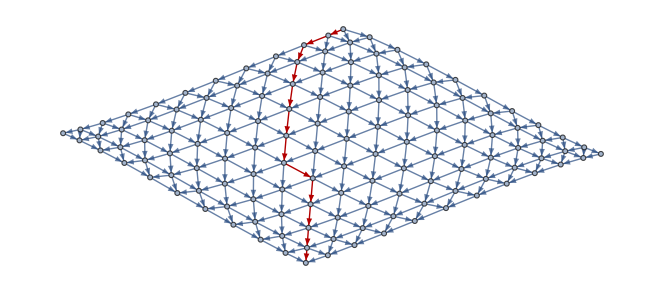

- | - | p | o | l | y | n | o | m | i | a | l
e | x | p | o | n | e | n | - | t | i | a | l

```mathematica
v=Table[{i,j},{i,0,10},{j,0,11}]//Flatten[#,1]&;
f[{x_,y_},{a_,b_}]:=(a==x+1&&y==b)||(a==x&&b==y+1)||(a==x+1&&b==y+1);
g=RelationGraph[f,v,DirectedEdges->True,VertexLabels->"Name",GraphLayout->"SpringEmbedding"];
g=Graph[EdgeList[g]/.a_->b_->Property[a->b,EdgeWeight->1]/.Property[{p_,q_}->{a_,b_},_]/;a==p+1&&b==q+1&&Characters[x][[a]]==Characters[y][[b]]->Property[{p,q}->{a,b},EdgeWeight->0]];
p=Partition[FindShortestPath[g,First@VertexList[g],Last@VertexList[g]],2,1];
HighlightGraph[g,p/.{a_,b_}->a->b]
fa[{{p_,q_},{a_,b_}}]:={Characters[x][[a]],"-"}/;a==p+1&&b==q;
fa[{{p_,q_},{a_,b_}}]:={"-",Characters[y][[b]]}/;a==p&&b==q+1;
fa[{{p_,q_},{a_,b_}}]:={Characters[x][[a]],Characters[y][[b]]}/;a==p+1&&b==q+1;
fa/@p//Transpose//TableForm
```

#### By MMA

```mathematica
EditDistance[x,y]
```

6

```mathematica
SequenceAlignment[x,y]
```

{{,ex},po,{ly,ne},n,{om,t},ial}

### Knapsack Problem with Replacement

```mathematica
ClearAll["Global`*"];
item={{6,30},{3,14},{4,16},{2,9}};
Kn[0]=0;
Kn[w_]:=Kn[w]=Module[{i,choices,best},
i=Select[item,#[[1]]≤w&]/.{}->{{w,0}};
choices={w-#[[1]],#[[2]]}&/@i;
Max[Kn[#[[1]]]+#[[2]]&/@choices]
];
Table[Kn[i],{i,0,10}]
```

{0,0,9,14,18,23,30,32,39,44,48}

### Knapsack Problem without Replacement

### Maximal Subsequence Problem

```mathematica
ClearAll["Global`*"];
l={5,15,-30,10,-5,40,10};
s[0]:=0;
s[i_]:=s[i]=Module[{choice,best},
choice={s[i-1]+l[[i]],l[[i]]};
best=Max[choice];
seq[i]={Append[seq[i-1],l[[i]]],{l[[i]]}}[[First@Flatten@Position[choice,best]]];
best
];
s[Length[l]]
seq[Length[l]]
```

55

{10,-5,40,10}

### River Crossing Puzzle

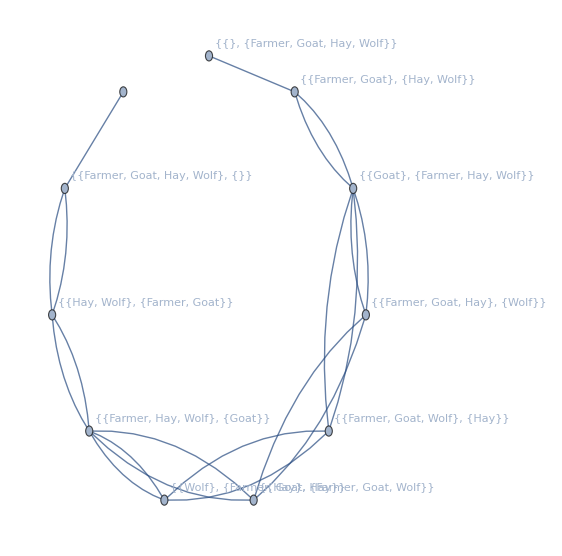

```mathematica
ClearAll["Global`*"];
allowedState={{"Hay","Wolf"},{"Hay"},{"Wolf"},{"Goat"},{}};
stateTranList[{t1_List,t2_List}]:=Module[{t,t3},
t=Complement[t1,{"Farmer"}]//Tuples[{{"Farmer"},#}]&//Append[#,{"Farmer"}]&;
t3={Sort@Complement[t1,#],Sort@Flatten@Append[t2,#]}&/@t;
Select[t3,MemberQ[allowedState,#[[1]]]&]
]/;MemberQ[t1,"Farmer"]
stateTranList[{t1_List,t2_List}]:=Reverse/@stateTranList[{t2,t1}]/;MemberQ[t2,"Farmer"]
stateTranString[t_String]:=Module[{t1,t2},
t1=Map[ToString,ToExpression[t],{2}];
t2=stateTranList[t1];
ToString/@t2
];
(* define the initial state *)
t1={"Farmer","Goat","Hay","Wolf"};t2={};
(* test state transition *)
(* stateTranString[MapAll[ToString,{t1,t2}]] *)
(* stateTranString[MapAll[ToString,{t2,t1}]] *)
(* state transition diagram *)
t=MapAll[ToString,{Sort@t1,Sort@t2}];
NestList[Flatten[Thread[#<->stateTranString[#]]&/@(Last/@#)]&,{""<->t},7];
Flatten[%,1]//DeleteDuplicates;
Graph[%,VertexLabels->"Name",GraphLayout->"CircularEmbedding"]
```

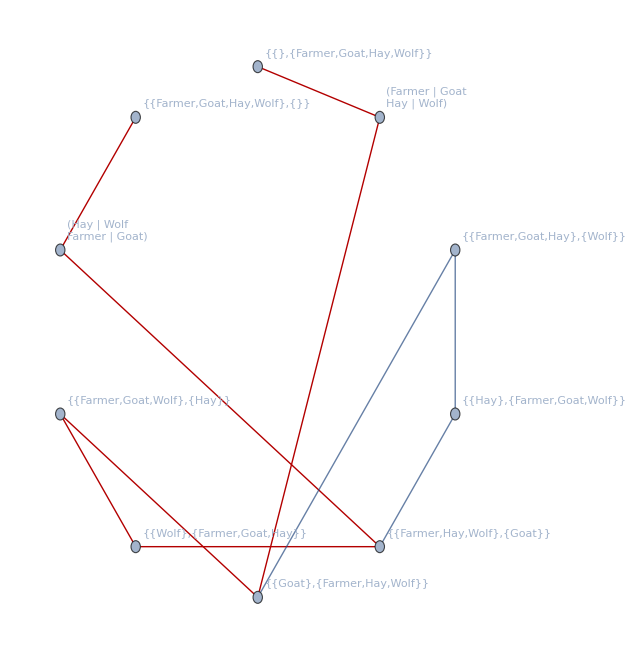

```mathematica
ClearAll["Global`*"];
(* create all states *)
s1={"Farmer","Wolf","Goat","Hay"};
s2=Table[HoldForm@Nothing,{i,4}];
t1=Sort/@Tuples[Transpose[{s1,s2}]]//ReleaseHold;
t2=Complement[s1,#]&/@%;
unfilteredStates=Thread[List[t1,t2]];
(* forbidden state *)
fsHelper[s_]:=(MemberQ[s,"Wolf"]∧MemberQ[s,"Goat"]∧¬MemberQ[s,"Farmer"]) ∨(MemberQ[s,"Hay"]∧MemberQ[s,"Goat"]∧¬MemberQ[s,"Farmer"]);
fs[{s1_,s2_}]:=¬(fsHelper[s1]∨fsHelper[s2]);
filteredStates=Select[unfilteredStates,fs];
(* s1 - t1 = t2 - s2 *)
tran[{{s1_,s2_},{t1_,t2_}}]:=Module[{T},
T=Complement[s1,t1];
Complement[s1,t1]==Complement[t2,s2]∧
1≤Length[Complement[s1,t1]]≤2∧
MemberQ[T,"Farmer"]∧
Intersection[s1,t1]==t1∧
Intersection[s2,t2]==s2
]/;MemberQ[s1,"Farmer"]∧MemberQ[t2,"Farmer"];
tran[{{s1_,s2_},{t1_,t2_}}]:=tran[{{s2,s1},{t2,t1}}]/;MemberQ[s2,"Farmer"]∧MemberQ[t1,"Farmer"];
tran[__]:=False;
Select[Subsets[filteredStates,{2}],tran]/.{x_,y_}->(x<->y);
g=Graph[%,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
(* find path *)
HighlightGraph[g,PathGraph[FindShortestPath[g,{{"Farmer","Goat","Hay","Wolf"},{}},{{},{"Farmer","Goat","Hay","Wolf"}}]]]
```